# Numerical methods for ⅈ u_t+1/2 u_xx+|u|^2 u=0 on a<x<b with periodic BC.

I thought I would see how well ChatGPT would do on our task at hand.   I changed N to n

```mathematica
(*Strang Splitting Fourier Solver for NLS on[-L,L]*)
ClearAll[StrangNLS]

StrangNLS[f_,L_,n_,dt_,nt_,kappa_]:=Module[{dx,x,k,u,uhat,step,j},
(*Spatial grid*)
dx=2 L/n;
x=Table[-L+j dx,{j,0,n-1}];
(*Fourier modes (Mathematica ordering)*)k=Join[Range[0,n/2-1],Range[-n/2,-1]]*(Pi/L);
(*Initial condition*)
u=f/@x;
(*One Strang step*)
step[u_]:=Module[{u1,uhat},
(*Half nonlinear step*)
u1=u*Exp[I*kappa*Abs[u]^2*dt/2];
(*Linear step in Fourier space*)
uhat=Fourier[u1];
uhat=uhat*Exp[-I*(k^2)*dt/2];
u1=InverseFourier[uhat];
(*Half nonlinear step*)
u1=u1*Exp[I*kappa*Abs[u1]^2*dt/2];
u1];
(*Time stepping*)
Do[u=step[u];,{j,1,nt}];
<|"x"->x,"u"->u|>]
```

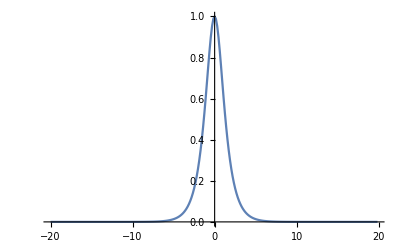

```mathematica
(*Example usage*)

L=20;
n=256;
dt=0.01;
nt=10; 
kappa=1;

f[x_]:=Sech[x];

result=StrangNLS[f,L,n,dt,nt,kappa];

xgrid=result["x"];
uFinal=result["u"];

ListLinePlot[Transpose[{xgrid,Abs[uFinal]}],PlotRange->All]

(*Optional:diagnostics*)

Mass[u_,dx_]:=dx Total[Abs[u]^2];

Energy[u_,k_,dx_,kappa_]:=Module[{uhat},uhat=Fourier[u];
dx Total[(k^2)*Abs[uhat]^2]/2-dx*kappa Total[Abs[u]^4]/2];

(*Track invariants over time*)
TrackSolution[f_,L_,n_,dt_,nt_,kappa_]:=Module[{dx,x,k,u,masses={},energies={},step,j},
dx=2 L/n;
x=Table[-L+j dx,{j,0,n-1}];
k=Join[Range[0,n/2-1],Range[-n/2,-1]]*(Pi/L);
u=f/@x;
step[u_]:=Module[{u1,uhat},
u1=u*Exp[I*kappa*Abs[u]^2*dt/2];
uhat=Fourier[u1];
uhat=uhat*Exp[-I*(k^2)*dt/2];
u1=InverseFourier[uhat];
u1=u1*Exp[I*kappa*Abs[u1]^2*dt/2];
u1];
Do[AppendTo[masses,Mass[u,dx]];
AppendTo[energies,Energy[u,k,dx,kappa]];
u=step[u];,{j,1,nt}];
<|"mass"->masses,"energy"->energies|>]
```

```mathematica
u
```

u